```mathematica
Fatt[x_,y_,bx_,by_] :=Module[{ρ (*distance point to obstacle*),Δρ (*gradient of ρ*)},
ρ=√((x-bx)^2+(-by+y)^2);
Δρ = {x-bx,y-by};
-Δρ /ρ
]
Frep[x_,y_,bx_,by_,α_] :=Module[{ρ (*distance point to obstacle*),Δρ (*gradient of ρ*), η=8 (*weighting factor*),ρ0=4(*radius of repulsion*),ϕ,angDiff},
ρ=√((-bx+x)^2+(-by+y)^2);
Δρ = {x-bx,y-by};
ϕ = ArcTan[x-bx,y-by];
angDiff = α-ϕ;
If[angDiff>π, angDiff=angDiff-2π];
If[angDiff<-π, angDiff=angDiff+2π];
If[ρ<ρ0&& Abs[angDiff]< π 7/8,Clip[ η(1/ρ - 1/ρ0)(1/ρ^2)Δρ ,{-1,1}],{0,0}]
]
r = 0.5;Manipulate[Module[{F},VectorPlot[F=Fatt[x,y,r Cos[α+π],r Sin[α+π]]+Frep[x,y,r Cos[α],r Sin[α],α];F/Norm[F],{x,-3,3},{y,-3,3},VectorPoints->Fine,StreamPoints->Coarse,StreamScale->Full,StreamStyle->Orange,Epilog-> {Blue,Thickness[0.01],Arrow[{{0,0},{Cos[α],Sin[α]}}]},Prolog->{Polygon[Table[1{Cos[a],Sin[a]},{a,0,2π,π/3}]]}]],{{α,0,"Desired direction"},0,2π}]
```

```mathematica
r = 0.5;Manipulate[VectorPlot[Frep[x,y,0,0,α],{x,-3,3},{y,-3,3},
Epilog-> {Blue,Thickness[0.01],Arrow[{{0,0},{Cos[α],Sin[α]}}]},Prolog->{Polygon[Table[1{Cos[a],Sin[a]},{a,0,2π,π/3}]]}],{α,0,2π}]
```

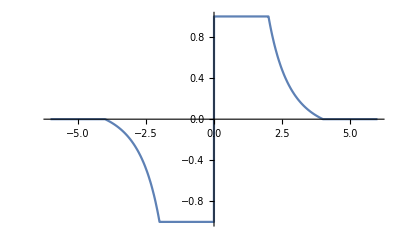

```mathematica
Plot[Clip[Frep[x,0,0,0]⟦1⟧,{-2,2}],{x,-6,6},PlotRange->All]
```

```mathematica
{a,b,0}×{c,d,0}
```

{0,0,-b c+a d}